```mathematica
ClearAll["Global`*"]
m=1;
l=20;
v=0.5;
g=9.8;
w=0.7;
A=1;
tmax=10;
w0 = Sqrt[g/l]
s=NDSolve[{m*l*theta''[t]+v theta'[t]+m g Sin[theta[t]]==A  Cos[w t],theta[0]==1,theta'[0]==0},theta,{t,0,tmax}];
```

0.7

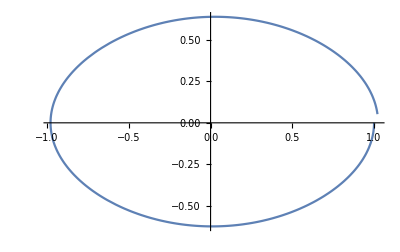

```mathematica
ParametricPlot[{theta[t],theta'[t]}/.s,{t,0,tmax}]
```

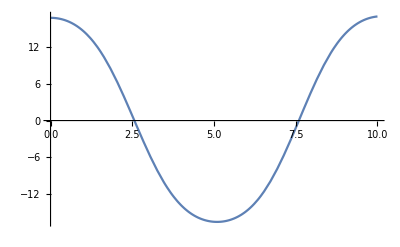

```mathematica
Plot[l*Sin[theta[t]]/.s,{t,0,tmax}]
```

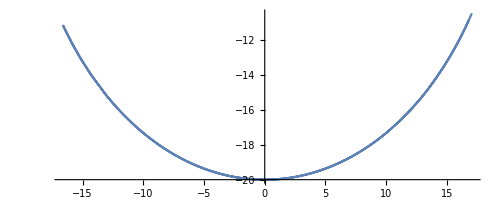

```mathematica
ParametricPlot[{l*Sin[theta[t]],-l*Cos[theta[t]]}/.s,{t,0,tmax}]
```

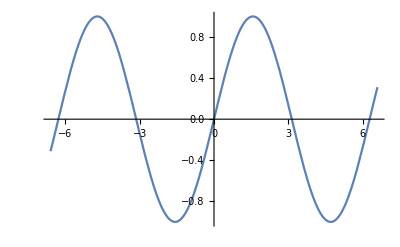

```mathematica
Plot[Sin[x], {x, -6.6, 6.6}]
```